```mathematica
β[ω_,δ_,t_,ϵ_]:=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[11],Join[Table[{i,i-1},{i,Range[2,11,1]}],Table[{i,i+1},{i,Range[1,11,1]}]]->-t]
```

```mathematica
T1[t_]:=ReplacePart[0*IdentityMatrix[11],Table[{2n,2n},{n,Range[1,5,1]}]->t]
```

```mathematica
T2[t_]:=ReplacePart[0*IdentityMatrix[11],Table[{2n-1,2n-1},{n,Range[1,6,1]}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,t,ϵ]],A:=Inverse[β[ω,δ,t,ϵ]],B:=Inverse[β[ω,δ,t,ϵ]],T1:=T1[t],T2:=T2[t]},Do[J=Inverse[IdentityMatrix[11]-A.T1.Inverse[IdentityMatrix[11]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

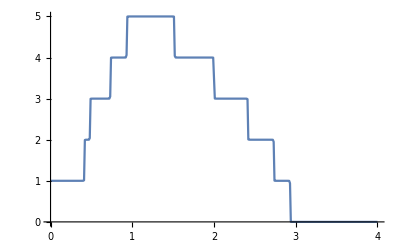
{94.6048,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[0,4,0.01]}]]]
```

```mathematica
ϕϕ1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{g:=Inverse[β[ω,δ,t,ϵ]],μ1=RandomInteger[{1,11}], μ2=RandomInteger[{1,11}], μ3=RandomInteger[{1,11}], μ4=RandomInteger[{1,11}],μ5=RandomInteger[{1,11}], μ6=RandomInteger[{1,11}], μ7=RandomInteger[{1,11}], μ8=RandomInteger[{1,11}]},
imp1=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*δ-ϵ1]]];imp3=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*δ-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*δ-ϵ1]]];imp5=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*δ-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*δ-ϵ1]]];imp7=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*δ-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,δ,t,ϵ]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*δ-ϵ1]]];Sl11:=Inverse[IdentityMatrix[11]-imp1.T1[1].SL[ω,δ,t,ϵ].T1[1]].imp1;
Sl12:=Inverse[IdentityMatrix[11]-imp2.T2[1].Sl11.T2[1]].imp2;
Sl13:=Inverse[IdentityMatrix[11]-imp3.T1[1].Sl12.T1[1]].imp3;
Sl14:=Inverse[IdentityMatrix[11]-imp4.T2[1].Sl13.T2[1]].imp4;
Sl15:=Inverse[IdentityMatrix[11]-imp5.T1[1].Sl14.T1[1]].imp5;
Sl16:=Inverse[IdentityMatrix[11]-imp6.T2[1].Sl15.T2[1]].imp6;
Sl17:=Inverse[IdentityMatrix[11]-imp7.T1[1].Sl16.T1[1]].imp7;
Sl18:=Inverse[IdentityMatrix[11]-imp8.T2[1].Sl17.T2[1]].imp8;
Il1:=Inverse[IdentityMatrix[11]-Sl18.T1[1].SR[ω,δ,t,ϵ].T1[1]].Sl18;
Ir1:=Inverse[IdentityMatrix[11]-SR[ω,δ,t,ϵ].T1[1].Sl18.T1[1]].SR[ω,δ,t,ϵ];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,t,ϵ].T1[1].Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]]
```

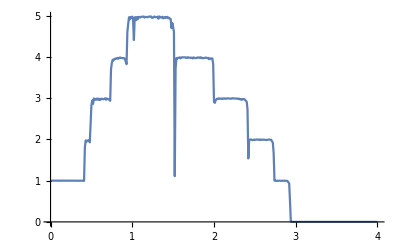
{5.45568,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[ϕϕ1[ω,0.001,1,0,.1]]},{ω,Range[0,4,0.01]}]]]
```

```mathematica
k81[ω_,ϵ1_]:=k81[ω,ϵ1]=Append[{},Table[ϕϕ1[ω,0.001,1,0,ϵ1],{i,1000}]]
```

```mathematica
ρ8[ω_,ϵ1_]:=Mean[k81[ω,ϵ1]]
```

```mathematica
Timing[Mean[ρ8[1.5,1]]]
```

{13.7142,1.05635}

```mathematica
Export["8imp3.csv",Table[{ω,Mean[ρ8[ω,0.3]]},{ω,Range[0,4,0.01]}]]
```

8imp3.csv

```mathematica
Export["8imp4.csv",Table[{ω,Mean[ρ8[ω,0.4]]},{ω,Range[0,4,0.01]}]]
```

8imp4.csv

```mathematica
Export["8imp5.csv",Table[{ω,Mean[ρ8[ω,0.5]]},{ω,Range[0,4,0.01]}]]
```

8imp5.csv

```mathematica
Export["8imp6.csv",Table[{ω,Mean[ρ8[ω,0.6]]},{ω,Range[0,4,0.01]}]]
```

8imp6.csv

```mathematica
Export["8imp7.csv",Table[{ω,Mean[ρ8[ω,0.7]]},{ω,Range[0,4,0.01]}]]
```

8imp7.csv

```mathematica
Export["8imp8.csv",Table[{ω,Mean[ρ8[ω,0.8]]},{ω,Range[0,4,0.01]}]]
```

8imp8.csv

```mathematica
Export["8imp9.csv",Table[{ω,Mean[ρ8[ω,0.9]]},{ω,Range[0,4,0.01]}]]
```

8imp9.csv

```mathematica
Export["8imp1.csv",Table[{ω,Mean[ρ8[ω,1]]},{ω,Range[0,4,0.01]}]]
```

8imp1.csv